## Finding

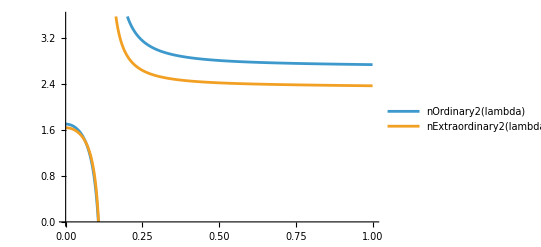

```mathematica
nOrdinary2[lambda_] = 2.7359 + 0.01878/(lambda^2-0.01822)-0.01354 lambda^2;
nExtraordinary2[lambda_] = 2.3753 + 0.01224/(lambda^2-0.01667)-0.01515 lambda^2;
Plot[{nOrdinary2[lambda], nExtraordinary2[lambda]}, {lambda, 0, 1}, PlotLegends->"Expressions", AxesOrigin->{0,0}]
```

```mathematica
nExtraordinary2[0.407]
```

2.45495

```mathematica
nOrdinary2[0.407]
```

2.86104

```mathematica
nOrdinary2[2 0.407]
```

2.75607

## Analytic check of state

```mathematica
A = N00 + N9090 - 2 N090;
dA = √((D[A,N00] √N00)^2 + (D[A,N9090] √N9090)^2 + (D[A,N090] √N090 )^2)
```

√(N00+4 N090+N9090)

```mathematica
thetal = ArcTan[√((N9090 - N090)/(N00 - N090))];
dthetal = √((D[thetal,N00] √N00)^2 + (D[thetal,N9090] √N9090)^2 + (D[thetal,N090] √N090 )^2) // CForm
```

Sqrt(N9090/(4.*(N00 - N090)*(-N090 + N9090)*Power(1 + (-N090 + N9090)/(N00 - N090),2)) + 
    (N00*(-N090 + N9090))/(4.*Power(N00 - N090,3)*Power(1 + (-N090 + N9090)/(N00 - N090),2)) + 
    ((N00 - N090)*N090*Power(-(1/(N00 - N090)) + (-N090 + N9090)/Power(N00 - N090,2),2))/(4.*(-N090 + N9090)*Power(1 + (-N090 + N9090)/(N00 - N090),2)))

```mathematica
cosphim = 1/Sin[2 thetal]((4 (N4545 - N090))/A-1)
dcosphim = √((D[cosphim,N00] √N00)^2 + (D[cosphim,N090] √N090)^2 + (D[cosphim,N9090] √N9090)^2+(D[cosphim,N4545] √N4545)^2) // CForm
```

(-1+(4 (-N090+N4545))/(N00-2 N090+N9090)) Csc[2 ArcTan[√((-N090+N9090)/(N00-N090))]]

Sqrt((16*N4545*Power(Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))),2))/Power(N00 - 2*N090 + N9090,2) + 
    N9090*Power((-4*(-N090 + N4545)*Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))))/Power(N00 - 2*N090 + N9090,2) - 
       ((-1 + (4*(-N090 + N4545))/(N00 - 2*N090 + N9090))*Cot(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090))))*Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))))/
        ((N00 - N090)*Sqrt((-N090 + N9090)/(N00 - N090))*(1 + (-N090 + N9090)/(N00 - N090))),2) + 
    N00*Power((-4*(-N090 + N4545)*Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))))/Power(N00 - 2*N090 + N9090,2) + 
       ((-N090 + N9090)*(-1 + (4*(-N090 + N4545))/(N00 - 2*N090 + N9090))*Cot(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090))))*
          Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))))/(Power(N00 - N090,2)*Sqrt((-N090 + N9090)/(N00 - N090))*(1 + (-N090 + N9090)/(N00 - N090))),2) + 
    N090*Power(((8*(-N090 + N4545))/Power(N00 - 2*N090 + N9090,2) - 4/(N00 - 2*N090 + N9090))*Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))) - 
       ((-1 + (4*(-N090 + N4545))/(N00 - 2*N090 + N9090))*(-(1/(N00 - N090)) + (-N090 + N9090)/Power(N00 - N090,2))*Cot(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090))))*
          Csc(2*ArcTan(Sqrt((-N090 + N9090)/(N00 - N090)))))/(Sqrt((-N090 + N9090)/(N00 - N090))*(1 + (-N090 + N9090)/(N00 - N090))),2))

## Computing

```mathematica
NN[alpha_, beta_] :=Switch[{alpha, beta},
{-45, -22.5}, N1,
{-45, 22.5}, N2,
{-45, 67.5}, N3,
{-45, 112.5}, N4,
{0, -22.5}, N5,
{0, 22.5}, N6,
{0, 67.5}, N7,
{0, 112.5}, N8,
{45, -22.5}, N9,
{45, 22.5}, N10,
{45, 67.5}, N11,
{45, 112.5}, N12,
{90, -22.5}, N13,
{90, 22.5}, N14,
{90, 67.5}, N15,
{90, 112.5}, N16
]
EE[alpha_, beta_]:= (NN[alpha, beta] + NN[alpha + 90, beta + 90] - NN[alpha, beta + 90] - NN[alpha + 90, beta])/(NN[alpha, beta] + NN[alpha + 90, beta + 90] + NN[alpha, beta + 90] + NN[alpha + 90, beta])
```

```mathematica
a = -45;
b = -22.5;
aa = 0;
bb = 22.5;
S = EE[a,b] - EE[a, bb] + EE[aa, b] + EE[aa, bb]
```

-(-N10+N12+N2-N4)/(N10+N12+N2+N4)+(-N13+N15+N5-N7)/(N13+N15+N5+N7)+(-N14+N16+N6-N8)/(N14+N16+N6+N8)+(N1+N11-N3-N9)/(N1+N11+N3+N9)

```mathematica
Serror = Sqrt[
N1 D[S,N1]^2
+N2 D[S,N2]^2
+N3 D[S,N3]^2
+N4 D[S,N4]^2
+N5 D[S,N5]^2
+N6 D[S,N6]^2
+N7 D[S,N7]^2
+N8 D[S,N8]^2
+N9 D[S,N9]^2
+N10 D[S,N10]^2
+N11 D[S,N11]^2
+N12 D[S,N12]^2
+N13 D[S,N13]^2
+N14 D[S,N14]^2
+N15 D[S,N15]^2
+N16 D[S,N16]^2
];
Serror // CForm
```

Sqrt(N12*Power((-N10 + N12 + N2 - N4)/Power(N10 + N12 + N2 + N4,2) - 1/(N10 + N12 + N2 + N4),2) + 
    N2*Power((-N10 + N12 + N2 - N4)/Power(N10 + N12 + N2 + N4,2) - 1/(N10 + N12 + N2 + N4),2) + 
    N10*Power((-N10 + N12 + N2 - N4)/Power(N10 + N12 + N2 + N4,2) + 1/(N10 + N12 + N2 + N4),2) + 
    N4*Power((-N10 + N12 + N2 - N4)/Power(N10 + N12 + N2 + N4,2) + 1/(N10 + N12 + N2 + N4),2) + 
    N13*Power(-((-N13 + N15 + N5 - N7)/Power(N13 + N15 + N5 + N7,2)) - 1/(N13 + N15 + N5 + N7),2) + 
    N7*Power(-((-N13 + N15 + N5 - N7)/Power(N13 + N15 + N5 + N7,2)) - 1/(N13 + N15 + N5 + N7),2) + 
    N15*Power(-((-N13 + N15 + N5 - N7)/Power(N13 + N15 + N5 + N7,2)) + 1/(N13 + N15 + N5 + N7),2) + 
    N5*Power(-((-N13 + N15 + N5 - N7)/Power(N13 + N15 + N5 + N7,2)) + 1/(N13 + N15 + N5 + N7),2) + 
    N14*Power(-((-N14 + N16 + N6 - N8)/Power(N14 + N16 + N6 + N8,2)) - 1/(N14 + N16 + N6 + N8),2) + 
    N8*Power(-((-N14 + N16 + N6 - N8)/Power(N14 + N16 + N6 + N8,2)) - 1/(N14 + N16 + N6 + N8),2) + 
    N16*Power(-((-N14 + N16 + N6 - N8)/Power(N14 + N16 + N6 + N8,2)) + 1/(N14 + N16 + N6 + N8),2) + 
    N6*Power(-((-N14 + N16 + N6 - N8)/Power(N14 + N16 + N6 + N8,2)) + 1/(N14 + N16 + N6 + N8),2) + 
    N3*Power(-((N1 + N11 - N3 - N9)/Power(N1 + N11 + N3 + N9,2)) - 1/(N1 + N11 + N3 + N9),2) + 
    N9*Power(-((N1 + N11 - N3 - N9)/Power(N1 + N11 + N3 + N9,2)) - 1/(N1 + N11 + N3 + N9),2) + 
    N1*Power(-((N1 + N11 - N3 - N9)/Power(N1 + N11 + N3 + N9,2)) + 1/(N1 + N11 + N3 + N9),2) + 
    N11*Power(-((N1 + N11 - N3 - N9)/Power(N1 + N11 + N3 + N9,2)) + 1/(N1 + N11 + N3 + N9),2))